# Load packages

```mathematica
SetDirectory[NotebookDirectory[]<>"../../package/"];
Get["funcs_rxns_moms.m"]
```

# Setup

```mathematica
nv=2;
nh=1;

volExp=14;
noIP3R=100;
cdir="../"<>getCacheDirRaw[volExp];

SetDirectory[NotebookDirectory[]];
dataDesc=importDataDesc[cdir<>"data_desc.txt"];
```

# Import data

## Import cache and transformations

```mathematica
SetDirectory[NotebookDirectory[]];

ip3s={"ip3_0p100","ip3_0p200","ip3_0p300","ip3_0p400","ip3_0p500","ip3_0p600","ip3_0p700","ip3_0p800","ip3_0p900","ip3_1p000","ip3_1p100","ip3_1p200","ip3_1p300","ip3_1p400","ip3_1p500","ip3_1p600","ip3_1p700","ip3_1p800","ip3_1p900","ip3_2p000"};

filtered0=Association[];
derivs0=Association[];
Monitor[
Do[
ip3=ip3s[[idx]];

pLFDL=Association[];
Do[
pLFDL[k]=Flatten[Import[cdir<>"filtered0/"<>ip3<>"/"<>k<>".txt","Table"]]
,{k,makeLF[nv,nh]}];

filtered0[ip3]=makePStructFromLFDL[nv,nh,pLFDL];

pLFDL=Association[];
Do[
pLFDL[k]=Flatten[Import[cdir<>"derivs0/"<>ip3<>"/"<>k<>".txt","Table"]]
,{k,makeLF[nv,nh]}];

derivs0[ip3]=makePStructFromLFDL[nv,nh,pLFDL];
,{idx,Length[ip3s]}];
,ProgressIndicator[idx,{1,Length[ip3s]}]]
```

```mathematica
pltEvery=10;
timesPlt=dataDesc["times"][[;;;;pltEvery]];
colors=Table[ColorData["BrownCyanTones"][i/Length[ip3s]],{i,Length[ip3s]}]
```

{RGBColor[0.4328202, 0.2875746, 0.16778140000000002],RGBColor[0.5179634, 0.3752862, 0.2504938],RGBColor[0.5943548, 0.45806840000000004, 0.33588],RGBColor[0.6619944, 0.5359212, 0.42394],RGBColor[0.729634, 0.613774, 0.512],RGBColor[0.7668376, 0.6736248, 0.5867076],RGBColor[0.8040412, 0.7334756, 0.6614152],RGBColor[0.8253242000000001, 0.787301, 0.7308212],RGBColor[0.8306866, 0.835101, 0.7949256],RGBColor[0.836049, 0.882901, 0.85903],RGBColor[0.8065450000000001, 0.9053942, 0.8961547999999999],RGBColor[0.777041, 0.9278874, 0.9332796],RGBColor[0.7376514, 0.9364448, 0.9557662],RGBColor[0.6883762, 0.9310664, 0.9636146],RGBColor[0.639101, 0.925688, 0.971463],RGBColor[0.585357, 0.8967528, 0.9580974],RGBColor[0.531613, 0.8678176000000001, 0.9447318],RGBColor[0.4723912, 0.8128028, 0.9049796],RGBColor[0.40769160000000004, 0.7317084, 0.8388408],RGBColor[0.342992, 0.650614, 0.772702]}

## Viz

## Vals

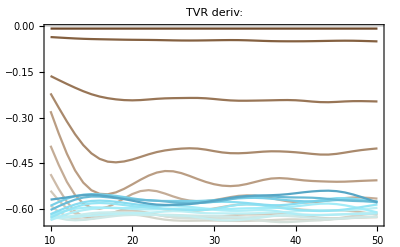
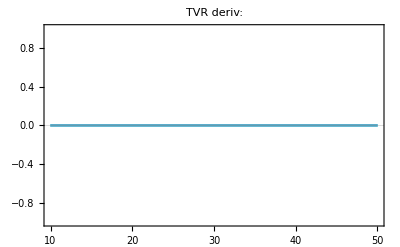
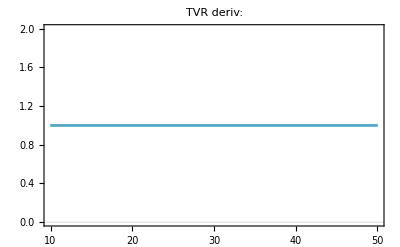
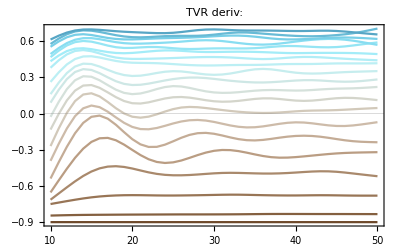
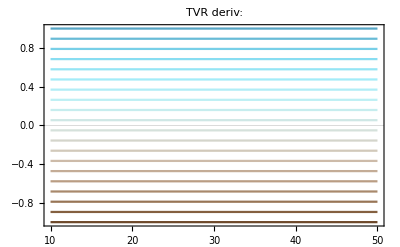
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | 0 | 0

```mathematica
plts=Table[
Show[
Table[
ip3=ip3s[[i]];
 xPlt=filtered0[ip3]["LFDL"][k][[;;;;pltEvery]];
ListLinePlot[Transpose[{timesPlt,xPlt}],PlotRange->All,PlotStyle->colors[[i]]]
,{i,Length[ip3s]}],
PlotRange->All,
PlotLabel->"TVR deriv: "<>labels[k],
FrameLabel->{"Time (s)"}
]
,{k,makeLF[nv,nh]}];
p=Grid[ArrayReshape[plts,{3,3}]]
```

## Derivs

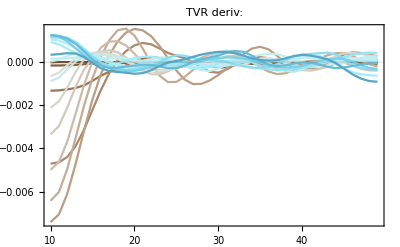
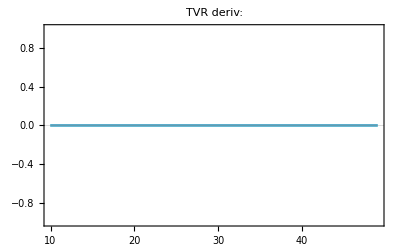
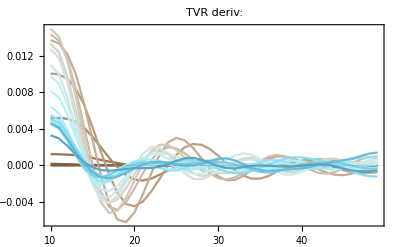
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | 0 | 0

```mathematica
plts=Table[
Show[
Table[
ip3=ip3s[[i]];
 xPlt=derivs0[ip3]["LFDL"][k][[;;;;pltEvery]];
ListLinePlot[Transpose[{timesPlt[[;;-2]],xPlt}],PlotRange->All,PlotStyle->colors[[i]]]
,{i,Length[ip3s]}],
PlotRange->All,
PlotLabel->"TVR deriv: "<>labels[k],
FrameLabel->{"Time (s)"}
]
,{k,makeLF[nv,nh]}];
p=Grid[ArrayReshape[plts,{3,3}]]
```

# Import graphs for STDs

```mathematica
tdir="training_data_rxns/";
```

```mathematica
SetDirectory[NotebookDirectory[]];
graphCalculateSTDs=Import[tdir<>"graph_calculate_stds.wlnet"];
graphInputsWOSTD=Import[tdir<>"graph_inputs_wo_std.wlnet"];
```

# Make & export training data

## Funcs

```mathematica
calculateStdsMVRandom[ip3sTrain_,dataDesc_,filtered0_,graphCalculateSTDs_,nRand_]:=Module[
{noTrainingData,inputsWOSTD,f0,in,rxnsSTDm,rxnsSTDv,keysAll,keysUse,key,i,tpt,ip3}
,

noTrainingData=Length[ip3sTrain]*dataDesc["noTpts"];
Print["Using ", nRand, " random pts out of ",noTrainingData," to estimate std params"];

keysAll=Flatten[Table[Table[{ip3,tpt},{tpt,dataDesc["noTpts"]}],{ip3,ip3sTrain}],1];
keysUse=RandomSample[keysAll,nRand];

inputsWOSTD=ConstantArray[0,nRand];

Monitor[
Do[
key=keysUse[[i]];
{ip3,tpt}=key;

f0=filtered0[ip3]["LD"];
in=<|
"wt"->f0[[tpt]]["wt"],
"b"->f0[[tpt]]["b"],
"sig2"->f0[[tpt]]["sig2"],
"tpt"->tpt
|>;
inputsWOSTD[[i]]=graphCalculateSTDs[in];

,{i,Length[keysUse]}];
,ProgressIndicator[i,{1,Length[keysUse]}]];

rxnsSTDm=Mean[inputsWOSTD];
rxnsSTDv=StandardDeviation[inputsWOSTD];

rxnsSTDm=Table[If[Abs[x]<10^-5,0.0,x],{x,rxnsSTDm}];
rxnsSTDv=Table[If[Abs[x]<10^-5,1.0,x],{x,rxnsSTDv}];

Return[{rxnsSTDm,rxnsSTDv}]
]
```

```mathematica
makeTrainingData[ip3sTrain_,noTpts_,derivs0_,filtered0_]:=Module[
{trainingData,idx,d0,f0,d0v}
,
trainingData=ConstantArray[0,Length[ip3sTrain]*(noTpts-1)];

idx=1;
Do[
d0=derivs0[ip3Key]["LD"];
f0=filtered0[ip3Key]["LD"];
Do[
d0v=Flatten[{d0[[tpt]]["b"],d0[[tpt]]["wt"],d0[[tpt]]["sig2"]}];

(* Zero *)
d0v=d0v[[{1,3}]];

trainingData[[idx]]=<|
"wt"->f0[[tpt]]["wt"],
"b"->f0[[tpt]]["b"],
"sig2"->{f0[[tpt]]["sig2"]},
"Output"->d0v,
"tpt"->{tpt}
|>;
idx+=1;
,{tpt,noTpts-1}];
,{ip3Key,ip3sTrain}];

Return[trainingData];
]
```

```mathematica
standardizeTraining[data_]:=Module[
{out,dataS,outMean,outStd,zeroCutoff,y}
,
out=Table[x["Output"],{x,data}];
outMean=Mean[out];
outStd=StandardDeviation[out];

zeroCutoff=10^-6;
outMean=Table[If[Abs[x]<zeroCutoff,0.0,x],{x,outMean}];
outStd=Table[If[Abs[x]<zeroCutoff,1.0,x],{x,outStd}];

dataS=Table[
y=x;
y["Output"]=(y["Output"]-outMean)/outStd;
y
,{x,data}];

Return[{dataS,outMean,outStd}]
]
```

```mathematica
standardizeValidation[data_,outMean_,outStd_]:=Module[
{dataS,y}
,
dataS=Table[
y=x;
y["Output"]=(y["Output"]-outMean)/outStd;
y
,{x,data}];

Return[dataS]
]
```

## Calculate STDs & export

```mathematica
ip3s
```

{ip3_0p100,ip3_0p200,ip3_0p300,ip3_0p400,ip3_0p500,ip3_0p600,ip3_0p700,ip3_0p800,ip3_0p900,ip3_1p000,ip3_1p100,ip3_1p200,ip3_1p300,ip3_1p400,ip3_1p500,ip3_1p600,ip3_1p700,ip3_1p800,ip3_1p900,ip3_2p000}

```mathematica
ip3sTrain={"ip3_0p400","ip3_0p500","ip3_0p600","ip3_0p700","ip3_0p800","ip3_0p900","ip3_1p000"};
ip3sTest={"ip3_0p100","ip3_0p200","ip3_0p300","ip3_1p100","ip3_1p200","ip3_1p300","ip3_1p400","ip3_1p500","ip3_1p600","ip3_1p700","ip3_1p800","ip3_1p900","ip3_2p000"};

Export[tdir<>"ip3s_train.txt",ip3sTrain,"Table","FieldSeparators"->" "]
Export[tdir<>"ip3s_test.txt",ip3sTest,"Table","FieldSeparators"->" "]

nRand=2807;
{rxnsSTDm,rxnsSTDv}=calculateStdsMVRandom[ip3sTrain,dataDesc,filtered0,graphCalculateSTDs,nRand]

SetDirectory[NotebookDirectory[]];
Export[tdir<>"std_m.txt",rxnsSTDm,"Table","FieldSeparators"->" "]
Export[tdir<>"std_v.txt",rxnsSTDv,"Table","FieldSeparators"->" "]
```

training_data_rxns/ip3s_train.txt

training_data_rxns/ip3s_test.txt

Using 2807 random pts out of 2807 to estimate std params

{{0.191856,-0.191856,0.0901285,-0.0901285,0.0901281,-0.191856,0.191856,-0.0901285,0.0901285,0.0901289,0.266659,0.0000149465,-0.550844,0.,-0.0606024,0.484706,0.0000149471,0.550844,0.,-0.0606027,0.0391694,-0.416874,0.,0.0000484808,0.0213176,0.0391694,0.294854,0.,-0.0000484806,0.0213176,-0.563197,0.,-0.11168,0.,-0.0558386,0.,0.0000499997,0.,-0.367022,-0.18351,-0.114266,0.0000100117,0.,0.,-0.0662204,0.563197,0.,0.11168,0.,-0.0558416,0.,-0.0000499997,0.,0.367022,-0.183513,-0.114266,0.0000100124,0.,0.,-0.0662204},{0.0920529,0.0920529,0.128815,0.128815,0.128815,0.0920529,0.0920529,0.128815,0.128815,0.128815,0.362709,1.,0.237401,1.,0.0571225,0.476181,1.,0.237401,1.,0.057123,0.0967364,0.282013,1.,0.211584,0.151859,0.0967364,0.407814,1.,0.211584,0.15186,0.0817631,1.,0.242898,1.,0.121449,1.,1.,1.,0.210566,0.105283,0.25361,0.0000221605,1.,1.,0.149922,0.0817631,1.,0.242898,1.,0.121449,1.,1.,1.,0.210566,0.105283,0.25361,0.0000221613,1.,1.,0.149922}}

training_data_rxns/std_m.txt

training_data_rxns/std_v.txt

## Make training data

```mathematica
trainingData=makeTrainingData[ip3sTrain,dataDesc["noTpts"],derivs0,filtered0];
validationData=makeTrainingData[ip3sTest,dataDesc["noTpts"],derivs0,filtered0];
 
Length[trainingData]
Length[validationData]
noOutput=Length[trainingData[[1]]["Output"]]
```

2800

5200

2

## Scale & export training data

{0.00070249,-0.000297816}

{0.00345636,0.00125536}

training_data_rxns/out_mean.txt

training_data_rxns/out_std.txt

training_data_rxns/training_data_s.mx

training_data_rxns/validation_data_s.mx

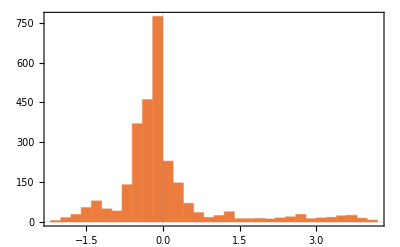
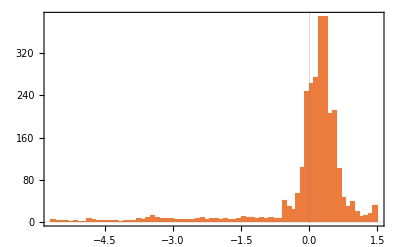

```mathematica
{trainingDataS,outMean,outStd}=standardizeTraining[trainingData];
outMean
outStd

validationDataS=standardizeValidation[validationData,outMean,outStd];

SetDirectory[NotebookDirectory[]];
Export[tdir<>"out_mean.txt",outMean,"Table","FieldSeparators"->" "]
Export[tdir<>"out_std.txt",outStd,"Table","FieldSeparators"->" "]

Export[tdir<>"training_data_s.mx",trainingDataS]
Export[tdir<>"validation_data_s.mx",validationDataS]

Table[
Histogram[Table[x["Output"][[i]],{x,trainingDataS}],PlotRange->All]
,{i,noOutput}]
```